```mathematica
Clear["Global`*"]
```

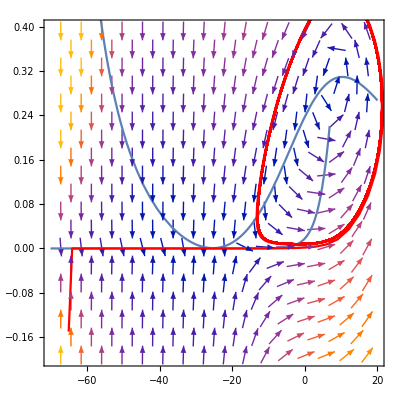

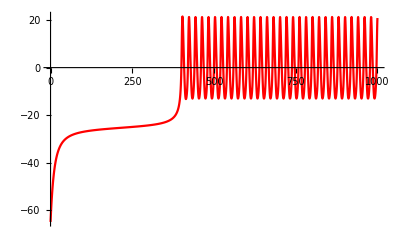

```mathematica
gna = 4.;(*mS/cm^2*)
u3 = 10.;(*mv*)
u4 = 10.;(*mv*)
una = 100.;(*mv*)
uk = -70.;(*mv*)
ul = -50.;(*mv*)
gk = 8.;(*mS/cm^2*)
gl = 2.;(*mS/cm^2*)
u1 = 0.;(*mv*)
u2 = 15.;(*mv*)
CM = 20.;(*uF/cm^2*)
Is =33;(*uA*)
(*模型微分表达式*)
minfty = 0.5*(1. + Tanh[(u - u1)/u2]);
ninfty = 0.5*(1. + Tanh[(u - u3)/u4]);
ϕ = 0.1*Cosh[(u - u3)/(2.*u4)];
du = (-gna*minfty*(u - una) - gk*n*(u - uk) - gl*(u - ul) + Is)/CM;
dn = ϕ*(ninfty - n);
(*nullclines零斜率线*)
lineu = (-gna*minfty*(u - una) - gl*(u - ul) + Is)/(gk*(u - uk));
linen = ninfty;
(*相图*)
vp = VectorPlot[{du, dn}, {u, -70, 20}, {n, -0.2, 0.4}, PlotRange -> All];
up = Plot[lineu, {u, -70, 20}];
np = Plot[linen, {u, -70, 20}];
sol = NDSolve[{u'[t] == (-gna*0.5*(1 + Tanh[(u[t] - u1)/u2])*(u[t] - una) - gk*n[t]*(u[t] - uk) - gl*(u[t] - ul) + Is)/CM, n'[t] == 0.1*Cosh[(u[t] - u3)/(2*u4)]*(0.5*(1 + Tanh[(u[t] - u3)/u4]) - n[t]), u[0] == -65, n[0] == -0.15}, {u, n}, {t, 0, 1000}];
pp = ParametricPlot[{u[t], n[t]} /. First@sol // Evaluate, {t, 0, 1000}, PlotRange -> All, PerformanceGoal -> "Quality", PlotStyle -> {Red}];
Show[{vp, up, np, pp}]
sol = NDSolve[{u'[t] == (-gna*0.5*(1 + Tanh[(u[t] - u1)/u2])*(u[t] - una) - gk*n[t]*(u[t] - uk) - gl*(u[t] - ul) + Is)/CM, n'[t] == 0.1*Cosh[(u[t] - u3)/(2*u4)]*(0.5*(1 + Tanh[(u[t] - u3)/u4]) - n[t]), u[0] == -65, n[0] == -0.15}, u, {t, 0, 1000}];
Plot[u[t] /. First@sol, {t, 0, 1000},PlotRange->All, PlotStyle -> {Red}]
```